```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]
```

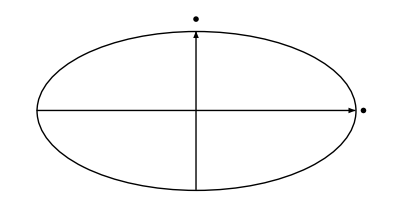

```mathematica
basicStatMechLecture4Fig4 = Graphics[{
Thick,
Circle[{0,0}, {2, 1}],
Arrow[{{-2,0},{2,0}}],
Arrow[{{0, -1},{0, 1}}],
Text[MaTeX["p"], {0, 1.15}],
Text[MaTeX["x"], {2.1, 0}]
}]
```

```mathematica
peeters`exportForLatex["basicStatMechLecture4Fig4",basicStatMechLecture4Fig4]
```

{basicStatMechLecture4Fig4.eps,basicStatMechLecture4Fig4pn.png}

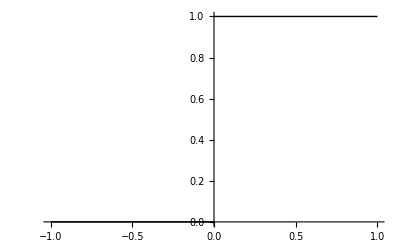

```mathematica
basicStatMechLecture6Fig2 = Plot[HeavisideTheta[x], {x, -1, 1}, PlotStyle-> {Thick, Black},
AxesLabel-> {MaTeX["x"], MaTeX["\\Theta(x)"]}]
```

```mathematica
peeters`exportForLatex["basicStatMechLecture6Fig2",basicStatMechLecture6Fig2]
```

{basicStatMechLecture6Fig2.eps,basicStatMechLecture6Fig2pn.png}

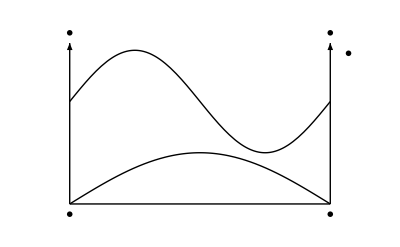

```mathematica
ClearAll[off, lecture7OneDSHOInBoxFig1]
off = 0.4;
l = Pi;
lecture7OneDSHOInBoxFig1 = Show[{
Plot[ { 2 + Sin[2x]}, {x,0,l}, PlotStyle->{Thick, Black}, Ticks -> None, Axes -> None,
PlotRange-> {{-off, l + off},{-off, l + off}}],
Plot[ {Sin[x]}, {x,0,l}, PlotStyle->{Thick, Black}, Ticks -> None, Axes -> None],
Graphics[{
Thick,
Arrow[{{0, 0},{0, l}}],
Line[{{0, 0},{l, 0}}],
Arrow[{{l, 0},{l, l}}],
Text[ MaTeX["0"], {0, -off/2}],
Text[ MaTeX["L"], {l, -off/2}],
Text[ MaTeX["\\infty"], {0, l + off/2}],
Text[ MaTeX["\\infty"], {l, l + off/2}],
Text[ MaTeX["V(x)"], {l +  0.55 off, l - off/2}]
}]}]
```

```mathematica
peeters`exportForLatex["lecture7OneDSHOInBoxFig1",lecture7OneDSHOInBoxFig1]
```

{lecture7OneDSHOInBoxFig1.eps,lecture7OneDSHOInBoxFig1pn.png}

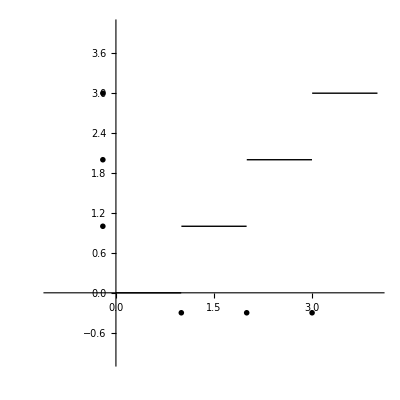

```mathematica
ClearAll[lecture71DquantumSHOStatesPerEnergyLevelFig4]

lecture71DquantumSHOStatesPerEnergyLevelFig4 = Show[{
Plot[HeavisideTheta[x-1] + HeavisideTheta[x - 2] + HeavisideTheta[x - 3] + HeavisideTheta[x - 4], {x, 0, 4},
Ticks -> None, 
PlotStyle-> {Thick, Black},
AxesLabel-> {MaTeX["E"], MaTeX["\\gamma"]},
PlotRange->{{-1, 4},{-1, 4}},
AspectRatio-> 1
],
Graphics[{
Text[MaTeX["\\hbar \\omega/2"], {1, -0.3}],
Text[MaTeX["3 \\hbar \\omega/2"], {2, -0.3}],
Text[MaTeX["5 \\hbar \\omega/2"], {3, -0.3}],
Text[MaTeX["1"], {-0.2, 1}],
Text[MaTeX["2"], {-0.2, 2}],
Text[MaTeX["3"], {-0.2, 3}]
}]
}]
```

```mathematica
peeters`exportForLatex["lecture71DquantumSHOStatesPerEnergyLevelFig4",lecture71DquantumSHOStatesPerEnergyLevelFig4]
```

{lecture71DquantumSHOStatesPerEnergyLevelFig4.eps,lecture71DquantumSHOStatesPerEnergyLevelFig4pn.png}